```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

(*Массив значений энергий*)
omegaVal={};

(*Интервал энергий*)
lowerBound =0.0;
upperBound=3;

step =0.1;

interval=Range[lowerBound,upperBound+step,step];

BSurf:=1.5*10^13;
R0:=12;

angleTheta:=Pi/3;
angleXi:=0Pi/6;
angleGamma:=Pi/4;

bR:=fDip*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Cos[angleTheta]);
bTheta:=gDip*0.5*BSurf*(R0/(z+R0))^3*(-Sin[angleXi]*Cos[angleTheta]*Cos[angleGamma]+Cos[angleXi]*Sin[angleTheta]);
bPhi:=gDip*0.5*BSurf*(R0/(z+R0))^3*(Sin[angleXi]*Sin[angleGamma]);

fDip:=-3/x^3(Log[1-x]+1/2 x(x+2));
gDip:=Sqrt[1-x](-2fDip+3/(1-x));
x:=4.134/(z+R0);

cosRotation:= bPhi/Sqrt[bPhi^2+bTheta^2]/.z->0;
sinRotation:=bTheta/Sqrt[bPhi^2+bTheta^2]/.z->0;

bRep:={bx->bTheta*sinRotation+bPhi*cosRotation,
	by->bTheta*cosRotation-bPhi*sinRotation,
	bz->bR};
	(*bPhi->BSurf*Cos[angleIteration]*(R0/(z+R0))^3};*)
(*0.5*BSurf*Sin[angleIteration]*(R0/(z+R0))^3*)

Bcrit:=4.4*10^13;
alpha:=1/137;


k0:=ω*5.06*10^9;
(*eV*5.06*10^9*)


B:={bx,by,bz};
Bunit:=B/Norm[B];

M:=((7 Bunit[[1]]^2 + 4 Bunit[[2]]^2)*μ[[1,1]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
n:=((4 Bunit[[1]]^2 + 7 Bunit[[2]]^2)*μ[[2,2]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
P:=(3μ[[1,1]]-4 delta (4 Bunit[[1]]^2 + 7 Bunit[[2]]^2))*Bunit[[1]]*Bunit[[2]]/
(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);

delta:=alpha/(45 Pi)*(Norm[B]^2/Bcrit^2);

Bmatrix:=Transpose[{B}].{B}/Norm[B]^2;
beta:=Norm[B]/Bcrit;

μ:=(1+a)*IdentityMatrix[3]+m *Bmatrix;

a:=-2 alpha/(9 Pi)*Log[1+beta^2*(1+0.25487*beta^(3/4))/(5*(1+0.75*beta^(5/4)))];
m:=-alpha/(3Pi)*beta^2/(3.75+2.7*beta^(5/4)+beta^2);

(*Параметры АЛП*)

g=6.01*10^(-20);
m=10^(-8);

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(4.134/R0))/(1-(4.134/(z+R0)))];

(*Без красного смещения*)
(*ω:=ω0;*)

(*Элементы матрицы М*)
deltaMx:=5.0*10^7*bx*g;
deltaMy:=5.0*10^7*by*g;

deltaMass:=2.5*10^9*m^2*(1/ω);

deltaCEDxx:=k0 delta M/2;
deltaCEDyy:=k0 delta n/2;
deltaCEDxy:=k0 delta P/2;
deltaCEDyx:=deltaCEDxy;

(*Матрица М*)
mat:={{  deltaCEDxx,deltaCEDxy,deltaMx    },
	{deltaCEDyx,deltaCEDyy,deltaMy    },
	{deltaMx       ,deltaMy      ,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
rmat[z_]:={{r11[z],r12[z],r13[z]},{r21[z],r22[z],r23[z]},{r31[z],r32[z],r33[z]}};

(*Список начальных условий*)
(*O-mode*)
rmat0={{r11[0]==1,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==0,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};
(*X-mode*)
(*rmat0={{r11[0]==0,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==1,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};*)

upperLimitSolve:=5000;

tSpectrum= Table[
(*Энергия на поверхности*)
ω0:=10^(k);
(*ω0:=k;*)

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(4.134/R0))/(1-(4.134/(z+R0)))];


(*Решаем систему*)
eqs=NDSolve[Join[{ⅈ rmat'[z]==rmat[z].mat-mat.rmat[z]/.bRep},rmat0],{r11[z],r22[z],r33[z]},{z,0,upperLimitSolve},MaxSteps->10^8, AccuracyGoal->5];
(*eqs=NDSolve[Join[{ⅈ rmat'[z]==rmat[z].mat-mat.rmat[z]/.bRep},rmat0],{r11[z],r22[z],r33[z]},{z,0,upperLimitSolve}];*)

Re[r11[z]+r22[z]/.First[eqs]/.z->(upperLimitSolve-1)]

,{k,interval}];


Print["Time elapsed: ",AbsoluteTime[]-time];

(*Строим ω с красным смещением*)
OmegaSurface:=10^x/.x->interval;
zFactor:=Sqrt[(1-(4.134/R0))];
OmegaInfinity1:=OmegaSurface*zFactor;
OmegaInfinity:=Log[10,OmegaInfinity1]

(*Строим график*)
data=Transpose[{OmegaInfinity,tSpectrum}];
plot = ListPlot[data,PlotRange->{{lowerBound,upperBound},{0.0,1.0}},PlotTheme->"Scientific",FrameStyle->Directive[GrayLevel[0],16,AbsoluteThickness[1.0]],FrameLabel->{Style["Log_10(ω_∞/eV)",16],Style["Λ",18]}, PlotMarkers->None,Joined->True,PlotStyle->{Thickness[.003]},InterpolationOrder->2]

(*Обычная шкала*)
(*dataToFile = Transpose[{10^x/.x->Range[lowerBound,upperBound,step],t}];*)

(*Логарифмическая шкала*)
dataToFile = Transpose[{OmegaInfinity,tSpectrum}];

(*Export["Mixing_m_t"<>ToString[mMult]<>"_p"<>ToString[mPower]<>"__g_t"<>ToString[gMult]<>"_p"<>ToString[gPower]<>".dat",dataToFile,"Table"];*)
(*Export["C:\\Users\\Алексей\\Documents\\Axions_RXJ_Paper\\References_for_paper\\Mixing_data\\Mixing_data.dat",dataToFile,"Table"];*)
```

Time elapsed: 5.9027252

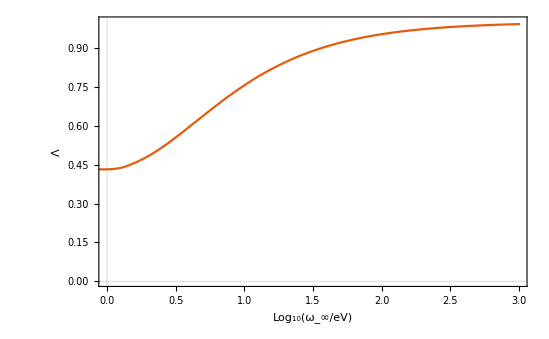

{{0,1,2,3,4,5},{10,11,12,13,14,15},{20,21,22,23,24,25},{30,31,32,33,34,35},{40,41,42,43,44,45},{50,51,52,53,54,55}}

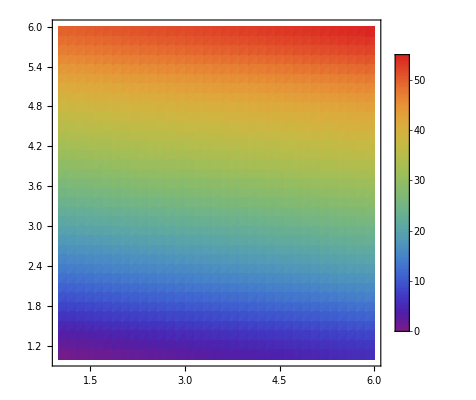

```mathematica
data=Table[10i+j,{i,0,5,1},{j,0,5,1}];
data
ListDensityPlot[data,Mesh->None,InterpolationOrder->2,ColorFunction->"Rainbow",PlotLegends->Automatic]
```